# B-Spline Schrodinger Equation Solver

## Nirav Mehta (Summer 2016)

## Bound States

First we’ll treat bound states for which ψ(x)→0 at x→±∞.  Solving the system in a box we will allow four kinds of boundary conditions at each boundary.  For example, at the left boundary:

Piecewise[{{LBC=0, ψ(x_left)=0}, {LBC=1, (ⅆψ/ⅆx)_x_left=0}, {LBC=2, open BC (no constraints)}, {LBC=3, (1/ψ ⅆψ/ⅆx)_xleft=k_left}}]

### Making the knot set

Our first goal is to construct the basis set.  We start with the knot set:

Let’s initialize some parameters:

```mathematica
xLinearGrid[xLeft_,xRight_,xNumPoints_]:=Module[{dx=(xRight-xLeft)/(xNumPoints-1)},Range[xLeft,xRight,dx]];
MakeKnots[LBC_,RBC_,xGrid_,BSOrder_]:=Module[{kn,xNumPoints=Length[xGrid],xL=xGrid[[1]],xR=xGrid[[Length[xGrid]]]},kn=PadRight[PadLeft[xGrid,xNumPoints+BSOrder,xL],xNumPoints+2BSOrder,xR];kn]
```

The dimension of the basis is:

```mathematica
xDim[Order_,xNumPoints_,LBC_,RBC_]:=Which[
LBC==2&&RBC==2,xNumPoints+Order-1,
LBC≠2&&RBC==2,xNumPoints+Order-2,
LBC==2&&RBC≠2,xNumPoints+Order-2,
LBC!=2&&RBC≠2,xNumPoints+Order-3
]
```

Now, we define a function to give the basis function for each left/right boundary condition.

```mathematica
MyBSpline[BSOrder_,xNumPoints_,Knots_,n_,x_,LBC_,RBC_]:=
Module[{result,kn,lk,xd},
lk=Length[Knots];
xd=xDim[BSOrder,xNumPoints,LBC,RBC];
Which[
LBC==2&&RBC==2,
	kn=Knots;
	result=BSplineBasis[{BSOrder,kn},n-1,x],
LBC==1&&RBC==1,
	kn=Knots;
	Which[
	n==1,
	result=BSplineBasis[{BSOrder,kn},0,x]+BSplineBasis[{BSOrder,kn},1,x],
	n==xd,
	result=BSplineBasis[{BSOrder,kn},xd+1,x]+BSplineBasis[{BSOrder,kn},xd,x],
	True,
	result=BSplineBasis[{BSOrder,kn},n,x]],
LBC==0&&RBC==0,
	kn=Knots[[2;;lk-1]];
	result=BSplineBasis[{BSOrder,kn},n-1,x],
LBC==0&&RBC==1,
	kn=Knots[[2;;lk]];
	If[n==xd,
	result=BSplineBasis[{BSOrder,kn},xd,x]+BSplineBasis[{BSOrder,kn},xd-1,x],
	result=BSplineBasis[{BSOrder,kn},n-1,x]],
LBC==1&&RBC==0,
	kn=Knots[[1;;lk-1]];
	If[n==1,
	result=BSplineBasis[{BSOrder,kn},0,x]+BSplineBasis[{BSOrder,kn},1,x], result=BSplineBasis[{BSOrder,kn},n,x]],
LBC==0&&RBC==2,
	kn=Knots[[2;;lk]];
	result=BSplineBasis[{BSOrder,kn},n-1,x],
LBC==2&&RBC==0,
	kn=Knots[[1;;lk-1]];
	If[n==1,
	result=BSplineBasis[{BSOrder,kn},0,x]+BSplineBasis[{BSOrder,kn},1,x],result=BSplineBasis[{BSOrder,kn},n-1,x]],
LBC==1&&RBC==2,
	kn=Knots[[1;;lk]];
	If[n==1,
	result=BSplineBasis[{BSOrder,kn},0,x]+BSplineBasis[{BSOrder,kn},1,x],result=BSplineBasis[{BSOrder,kn},n,x]],
LBC==2&&RBC==1,
	kn=Knots[[1;;lk]];
	If[n==xd,
	result=BSplineBasis[{BSOrder,kn},xd,x]+BSplineBasis[{BSOrder,kn},xd-1,x],result=BSplineBasis[{BSOrder,kn},n-1,x]]
];result]
```

{0,0,0,0,0,0,1,2,3,4,5,6,7,8,9,10,10,10,10,10,10}

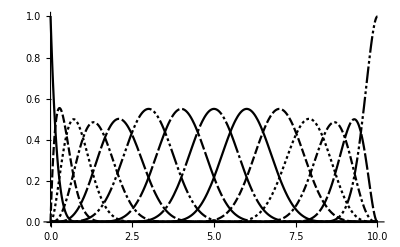

```mathematica
LBC=2;RBC=1;BSOrder=5;xNumPoints=11;xLeft=0;xRight=10;xGrid=xLinearGrid[xLeft,xRight,xNumPoints];knots=MakeKnots[LBC,RBC,xGrid,BSOrder]
Plot[Evaluate[Table[MyBSpline[BSOrder,xNumPoints,knots,i,x,LBC,RBC],{i,1,xDim[BSOrder,xNumPoints,LBC,RBC]}]],{x,xLeft,xRight},PlotRange->All]
```

```mathematica
xDim[BSOrder,xNumPoints,LBC,RBC]
```

14

```mathematica
MyBSpline[BSOrder,xNumPoints,knots,7,7.9,LBC,RBC]
```

0

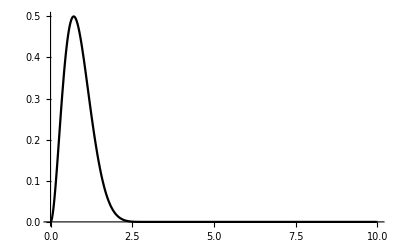

```mathematica
Plot[MyBSpline[BSOrder,xNumPoints,knots,3,x,LBC,RBC],{x,0,10},PlotRange->All]
```

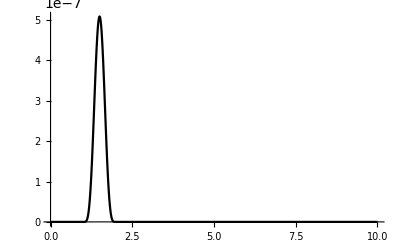

```mathematica
Plot[Evaluate[MyBSpline[BSOrder,xNumPoints,knots,7,x,LBC,RBC]MyBSpline[BSOrder,xNumPoints,knots,2,x,LBC,RBC]],{x,xLeft,xRight},PlotRange->All]
```

|

Now let’s fill the array of xBounds

```mathematica
MakexBounds[LBC_,RBC_,xNumPoints_,Knots_]:=
```

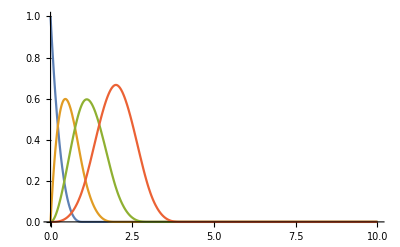

```mathematica
LBC=2;RBC=1;BSOrder=3;xNumPoints=11;xLeft=0;xRight=10;xGrid=xLinearGrid[xLeft,xRight,xNumPoints];knots=MakeKnots[LBC,RBC,xGrid,BSOrder];
iinit=1;
Plot[Evaluate[Table[MyBSpline[BSOrder,xNumPoints,knots,i,x,LBC,RBC],{i,iinit,iinit+BSOrder}]],{x,xLeft,xRight},PlotRange->All]
```

Cool.  It seems to be working for the standard boundary conditions.  I’ll come back to the Bethe-Pierles boundary condition later.

### Scratch work....

```mathematica
MyBSpline00[BSOrder_,xNumPoints_,Knots_,n_,x_]:=Module[{result,lk},
lk=Length[Knots];
result=BSplineBasis[{BSOrder,Knots[[2;;lk-1]]},n-1,x];
result
]
```

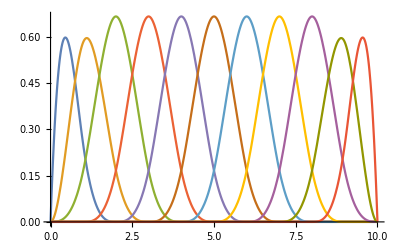

```mathematica
Plot[Evaluate[Table[MyBSpline00[BSOrder,xNumPoints,knots,i,x],{i,1,xDim[BSOrder,xNumPoints,0,0]}]],{x,xLeft,xRight},PlotRange->All]
```

```mathematica
MyBSpline22[BSOrder_,xNumPoints_,Knots_,n_,x_]:=Module[{result,lk},
lk=Length[Knots];
result=BSplineBasis[{BSOrder,Knots[[1;;lk]]},n-1,x];
result
]
```

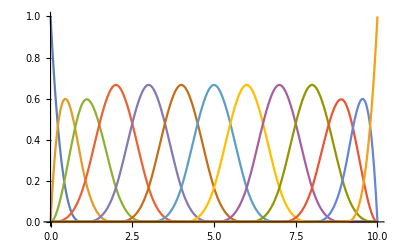

```mathematica
Plot[Evaluate[Table[MyBSpline22[BSOrder,xNumPoints,knots,i,x],{i,1,xDim[BSOrder,xNumPoints,2,2]}]],{x,xLeft,xRight},PlotRange->All]
```

```mathematica
MyBSpline01[BSOrder_,xNumPoints_,Knots_,n_,x_]:=Module[{result,lk},
lk=Length[Knots];
If[n==xDim[BSOrder,xNumPoints,0,1],
	result=BSplineBasis[{BSOrder,Knots[[2;;lk]]},n,x]+BSplineBasis[{BSOrder,Knots[[2;;lk]]},n-1,x],result=BSplineBasis[{BSOrder,Knots[[2;;lk]]},n-1,x]];
result
]
```

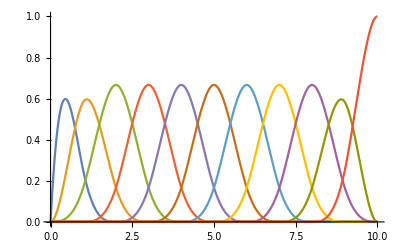

```mathematica
Plot[Evaluate[Table[MyBSpline01[BSOrder,xNumPoints,knots,i,x],{i,1,xDim[BSOrder,xNumPoints,0,1]}]],{x,xLeft,xRight},PlotRange->All]
```

```mathematica
MyBSpline10[BSOrder_,xNumPoints_,Knots_,n_,x_]:=Module[{result,lk},
lk=Length[Knots];
If[n==1,
	result=BSplineBasis[{BSOrder,Knots[[1;;lk-1]]},0,x]+BSplineBasis[{BSOrder,Knots[[1;;lk-1]]},1,x],result=BSplineBasis[{BSOrder,Knots[[2;;lk-1]]},n-1,x]];
result
]
```

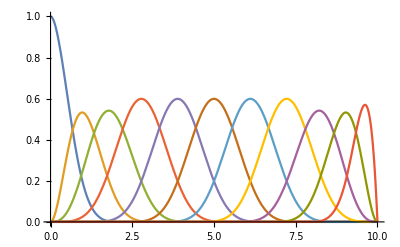

```mathematica
Plot[Evaluate[Table[MyBSpline10[BSOrder,xNumPoints,knots,i,x],{i,1,xDim[BSOrder,xNumPoints,1,0]}]],{x,xLeft,xRight},PlotRange->All]
```

```mathematica
MyBSpline11[BSOrder_,xNumPoints_,Knots_,n_,x_]:=Module[{result,lk},
lk=Length[Knots];
Which[
n==1,
result=BSplineBasis[{BSOrder,Knots[[1;;lk]]},0,x]+BSplineBasis[{BSOrder,Knots[[1;;lk]]},1,x],
n==xDim[BSOrder,xNumPoints,1,1],
result=BSplineBasis[{BSOrder,Knots[[1;;lk]]},n+1,x]+BSplineBasis[{BSOrder,Knots[[1;;lk]]},n,x],True,
result=BSplineBasis[{BSOrder,Knots[[1;;lk]]},n,x]];
result
]
```

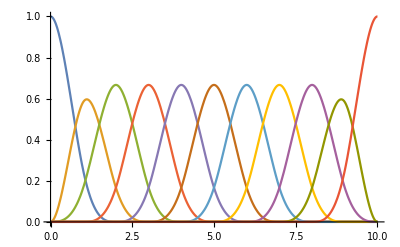

```mathematica
Plot[Evaluate[Table[MyBSpline11[BSOrder,xNumPoints,knots,i,x],{i,1,xDim[BSOrder,xNumPoints,1,1]}]],{x,xLeft,xRight},PlotRange->All]
```

For the “3” boundary condition we wish to allow for arbitrary log-derivative at the boundary.  We therefore let the (first) last B-spline be an arbitrary linear combination of the (first two) last two B-splines implied by the full knot sequence.  For example, at the left boundary:

((ψ'(x))/(ψ(x)))_(x=x_l)=K_l=((C_1(∂B_1(x))/(∂x)+C_2(∂B_2(x))/(∂x))/(C_1 B_1(x)+C_2 B_2(x)))_(x=x_l)

Now we use the fact that only B_1(x_l)=1, while B_2 and indeed all other B_n vanish at x=x_l.

K_l=((C_1/C_2(∂B_1(x))/(∂x)+(∂B_2(x))/(∂x))/(C_1/C_2B_1(x)))_(x=x_l)

C_1/C_2=C_l=((∂B_2(x_l))/(∂x))/(K_l B_1(x_l)-(∂B_1(x_l))/(∂x))

This amounts to letting the left-most B-spline be

OverTilde[B_l](x)=C_l B_1+B_2,   C_l=C_1/C_2

Similarly for the right-most B-spline

OverTilde[B_r](x)=B_(N-1)+C_r B_N(x),  C_r=C_N/(C_(N-1))

K_r=((ψ'(x))/(ψ(x)))_(x=x_r)=(((B̃')_r)/((B̃)_r))_x_r=((∂B_(N-1)(x_r))/(∂x)+C_r(∂B_N(x_r))/(∂x))/(B_(N-1)(x_r)+C_r B_N(x_r))

But now only B_N is nonzero at the right boundary

K_r=((∂B_(N-1)(x_r))/(∂x)+C_r(∂B_N(x_r))/(∂x))/(C_r B_N(x_r))

C_r=((∂B_(N-1)(x_r))/(∂x))/(K_r B_N(x_r)-(∂B_N(x_r))/(∂x))

Note that alternatively, one may rescale (B̃)_r by dividing by C_r: OverTilde[B_r](x)→ 1/C_r B_(N-1)+B_N(x), which simply amounts to changing the overall scale of the basis function.  This ends up being more numerically stable, since it still ensures that the value of the basis function approaches 1 at the edge.

```mathematica
MyBSpline33[BSOrder_,xNumPoints_,Knots_,Kl_,Kr_,n_,x_]:=Module[{result,lk,xd,kn,Cl,Cr,xL,xR},
lk=Length[Knots];
xL=Knots[[1]];
xR=Knots[[lk]];
kn=Knots[[1;;lk]];
xd=xDim[BSOrder,xNumPoints,1,1];
Cl=D[BSplineBasis[{BSOrder,kn},1,x],{x,1}]/(Kl BSplineBasis[{BSOrder,kn},0,x]-D[BSplineBasis[{BSOrder,kn},0,x],{x,1}])/.x->xL;
Cr=D[BSplineBasis[{BSOrder,kn},xd,x],{x,1}]/(Kr BSplineBasis[{BSOrder,kn},xd+1,x]-D[BSplineBasis[{BSOrder,kn},xd+1,x],{x,1}])/.x->xR;
Which[
	n==1,
	result= BSplineBasis[{BSOrder,kn},0,x]+1/Cl BSplineBasis[{BSOrder,kn},1,x],
	n==xd,
	result= BSplineBasis[{BSOrder,kn},xd+1,x]+1/Cr BSplineBasis[{BSOrder,kn},xd,x],
	True,
	result=BSplineBasis[{BSOrder,kn},n,x]]
]
```

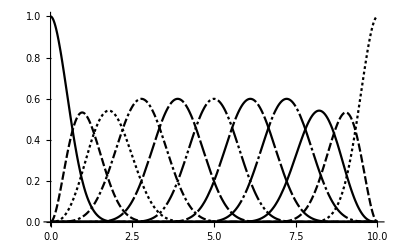

```mathematica
Plot[Evaluate[Table[MyBSpline33[BSOrder,xNumPoints,knots,0,0,i,x],{i,1,xDim[BSOrder,xNumPoints,1,1]}]],{x,xLeft,xRight},PlotRange->All]
```